# MAT: 150 -- Lab 3

## Date: 9/22/2017 Due: 9/25/2017

## 2D Vector Graphics

Recall our modest spaceship from class, which we define in homogenous coordinates below.

```mathematica
T={{0,2,1},{0,0,3},{1,1,1}};
```

When displaying the spaceship, we will use the Graphics and Triangle command. The latter is expecting three points, which correspond to the three columns of T, but only including the first 2 rows. We can do this as follows (note the use of the help function, to simplify the Graphics command).

```mathematica
help[T_]:=Triangle[{T[[1;;2,1]],T[[1;;2,2]],T[[1;;2,3]]}];
```

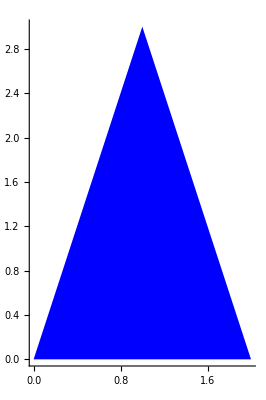

```mathematica
Graphics[{Blue,help[T]},Axes->True]
```

### Translation

To move our spaceship vertically and horizontally, we will make use of the fact that a translation can be represented as a linear transformation in the homogenous coordinate system.

```mathematica
trans[T_,r_,s_]:= {{1,0,r},{0,1,s},{0,0,1}}.T;
```

We can get a sense for what these translations will look like using Manipulate (animate but without the auto play). The blue triangle is the original, the red is the translated triangle.

```mathematica
Manipulate[Graphics[{Blue,help[T],Red, help[trans[T,r,s]]},Axes->True],{r,-2,2},{s,-2,2}]
```

### Rotation

In order to rotate our spaceship about its center (centroid), we need to compose a translation and its inverse with a rotation as follows.

```mathematica
mid[T_]:=RegionCentroid[help[T]];
```

The function mid uses RegionCentroid to compute the centroid of the Triangle represented by T, note that this function will work for more general regions as well.

```mathematica
rot[T_,t_]:=
Module[{r,s,Q},
r=mid[T][[1]];
s=mid[T][[2]];
Q={{Cos[t],-Sin[t],0},{Sin[t],Cos[t],0},{0,0,1}};
trans[Q.trans[T,-r,-s],r,s]]
```

Again, we will get a sense for this transformation using animate.

```mathematica
Manipulate[Graphics[{Blue,help[T],Red,help[rot[T,t]]},Axes->True],{t,0,2*Pi}]
```